Ans to the question 5(c):

```mathematica
NDSolve[{x''[t]+x[t]==0,x[0]==1,x'[0]== 0},{x[t],x'[t]},{t,0,10 π}]
```

{{x[t]→InterpolatingFunction[…][t],x'[t]→InterpolatingFunction[…][t]}}

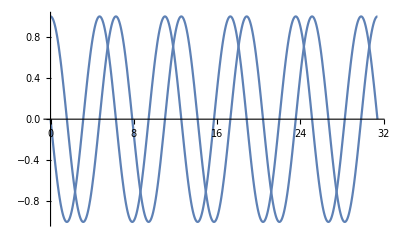

```mathematica
Plot[{x[t],x'[t]}/.%11,{t,0,10π}]
```